```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
hfE = -7.862132; (* THIS MAY BE WRONG NOW *)
gsE = -7.8807866389;
```

```mathematica
eigvals =Get["spectrum_data.txt"]["eigvals"];
gsE = First @ eigvals
```

-7.88079

```mathematica
styling = {
	ImageSize->Medium,
	LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
	Frame->True,FrameStyle->Black,
	FrameTicks->{{Automatic,None},{Automatic,None}},
	GridLinesStyle -> Directive[Dashed,Gray,Thin],
	GridLines->  {None,{
		{gsE,Directive[Red,Dashing[None],Thick]}, 
		{hfE,Directive[Red,Dashed,Thick]},
		Sequence @@ eigvals[[2;;]]
	}},
	PlotStyle -> {RGBColor[0,.72,1], RGBColor[.92,.59,.18]},
	PlotLegends -> Placed[
		LineLegend[
			{RGBColor[0,.72,1], RGBColor[.92,.59,.18], Directive[Red,Dashed],Red},
			{" Imaginary time", " Gradient descent", " Hartree Fock", " Ground"},
			LegendMarkerSize->20, Spacings -> .1
		], {.75,.7}]
};
```

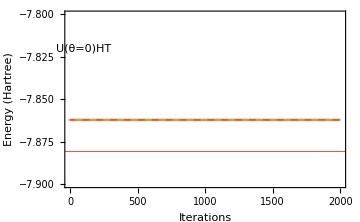

```mathematica
dataHT = Get["output_HT.txt"];
htplot = ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.8},
	FrameLabel->{"Iterations","Energy (Hartree)"},
	PlotLegends->None,
	Sequence @@ styling,

	Epilog -> Style[Text["U(θ=0)HT",{100,-7.82}], 12,FontFamily->"Latin Modern Roman"]
]
```

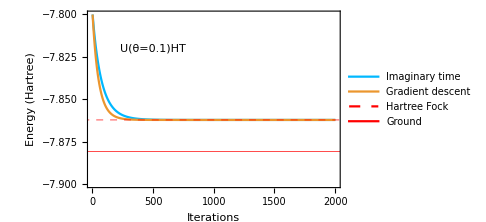

```mathematica
dataNearHT = Get["output_nearHT.txt"];
htplot = ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.8},
	FrameLabel->{"Iterations","Energy (Hartree)"},
	Sequence @@ styling,

	Epilog -> Style[Text["U(θ=0.1)HT",{500,-7.82}], 12,FontFamily->"Latin Modern Roman"]
]
```

```mathematica
dataHT = Get["output_HT.txt"];
htplot = ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.8},
	FrameLabel->{"Iterations","Energy (Hartree)"},
	PlotLegends->None,
	Sequence @@ styling,

	Epilog -> Style[Text["U(θ=0)HT",{100,-7.82}], 12,FontFamily->"Latin Modern Roman"]
];

dataNearHT = Get["output_nearHT.txt"];
nearhtplot = ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.8},
	FrameLabel->{None,"Energy (Hartree)"},
	Sequence @@ styling,
	
	Epilog -> Style[Text["U(θ=.1)HT",{100,-7.82}], 12,FontFamily->"Latin Modern Roman"]
];

Column[{
 nearhtplot,htplot
}, Spacings->-2.4]
```

ListLinePlot::nonopt: Options expected (instead of styling) beyond position 1 in ListLinePlot[{{-4.76122,-4.76463,-4.76814,-4.77177,-4.77552,-4.77938,-4.78334,-4.78743,-4.79165,«33»,-5.03514,-5.04628,-5.05767,-5.06932,-5.08122,-5.09338,-5.10579,-5.11846,«1951»},{«1»}},«4»,Epilog→«1»]. An option must be a rule or a list of rules.

Get::noopen: Cannot open output_nearHT.txt.

ListLinePlot::nonopt: Options expected (instead of styling) beyond position 1 in ListLinePlot[{$Failed[imagEnergies],$Failed[gradEnergies]},PlotRange→{-7.9,-7.8},FrameLabel→{None,Energy (Hartree)},styling,Epilog→Text[U(θ=.1)HT,{100,-7.82}]]. An option must be a rule or a list of rules.

```mathematica
Export["nearHT.pdf",%]
```

nearHT.pdf

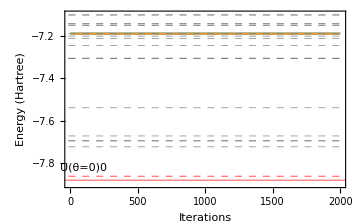

```mathematica
dataZero = Get["output_zero.txt"];
htplot = ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.1},
	FrameLabel->{"Iterations","Energy (Hartree)"},
	PlotLegends->None,
	Sequence @@ styling,

	Epilog -> Style[Text["U(θ=0)0",{100,-7.82}], 12,FontFamily->"Latin Modern Roman"]
]
```

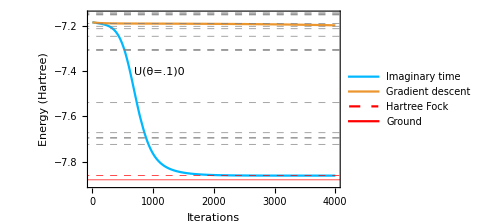

```mathematica
dataNearZero = Get["output_nearZero_extended.txt"];
ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.15},
	FrameLabel->{"Iterations","Energy (Hartree)"},
	Sequence @@ styling,
	
Epilog -> Style[Text["U(θ=.1)0",{1100, -7.4}], 12,FontFamily->"Latin Modern Roman"]
]
```

```mathematica
Export["nearZero.pdf", %]
```

nearZero.pdf